# Trivial Equilibria Stability Analysis

```mathematica
ClearAll[ϕ,ψ,A,B,ϕPrime,psiPrime,APrime,BPrime,dA,dB,p,b,m,s,Da,Db];
F[A_,B_]:=-dA*A+m*B+2*p*A*B
G[A_,B_]:=B*(-dB-m-2*p*A+2*b-2*b*(A+B))
M ={{Da*(1-B)+p*B,Da*A,0,0},{Db*B,Db*(1-A)-b*(A+B),0,0},{0,0,1,0},{0,0,0,1}};
(*Vector on the right-hand side*)
Inverse[M] //MatrixForm;
RHS:={-s*ϕ-F[A,B],-s*ψ-G[A,B],ϕ,ψ};
(*Isolating derivatives on the right hand-side {phiPrime,psiPrime,APrime,BPrime}*)
LHS:=Inverse[M].RHS
(*Solve for derivatives when {phi',psi',A',B'}=0*)
EquilibriaEquation := LHS == {0,0,0,0};
equilibria = Solve[EquilibriaEquation, {ϕ, ψ, A, B}];
(*Returning the trivial equilibria(0,0,0,0)*)
trivialEquilibrium := equilibria [[1]]
```

```mathematica
(*Find the Jacobian of the system *)
JacMatrix = D[LHS,{{ϕ,ψ,A,B}}];
ParamReplacements := {Da->0.1,Db->0.1, D->0.1,p->0.2,dA->0.01, dB->0.01 ,m->0.001};
EpsReplacements := {Da -> ϵ, Db -> ϵ, dA ->ϵ^2, dB -> ϵ^2, m -> ϵ^3}
NumJacMatrix = FullSimplify[JacMatrix /. ParamReplacements];
EpsJacMatrix = JacMatrix /. EpsReplacements //MatrixForm;
```

```mathematica
TrivialEqJacob := JacMatrix /. trivialEquilibrium
TrivialEqJacob //MatrixForm
(*TrivialEqJacob /.ParamReplacements //MatrixForm
TrivialEqJacob /.EpsReplacements // MatrixForm*)
```

(-s/Da | 0 | dA/Da | -m/Da
0 | -s/Db | 0 | (-2 b+dB+m)/Db
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

```mathematica
EigenTrivial := Eigenvalues[TrivialEqJacob]
```

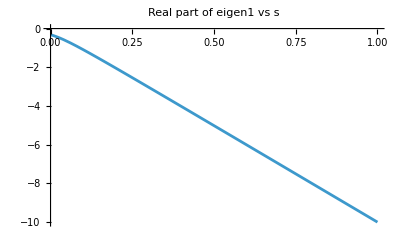

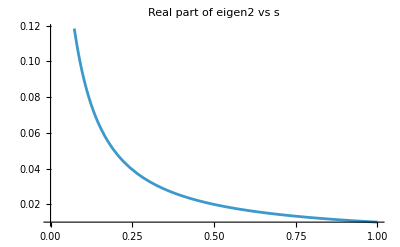

-Graphics3D-

-Graphics3D-

```mathematica
eigen1[b_,s_]:= EigenTrivial[[1]] /. ParamReplacements;
eigen2[b_,s_]:= EigenTrivial[[2]] /. ParamReplacements;
eigen3[b_,s_]:= EigenTrivial[[3]] /. ParamReplacements;
eigen4[b_,s_]:= EigenTrivial[[4]] /. ParamReplacements;

Plot[Re[eigen1[b,s]],{s,0,1},PlotLabel->"Real part of eigen1 vs s"]
Plot[Re[eigen2[b,s]],{s,0,1},PlotLabel->"Real part of eigen2 vs s"]
Plot3D[
 Re[eigen3[b, s]],
 {b, 0, 1}, {s, 0, 1},
 PlotLabel -> "Real part of eigen3 vs b and s",
 AxesLabel -> {"b", "s", "Re[eigen3]"},
 ColorFunction -> Function[{x, y, z}, 
    Which[
      z > 0, Green, 
      z < 0, Red, 
      True, Yellow
    ]
  ], 
 ColorFunctionScaling -> False,
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}}
]

Plot3D[
 Re[eigen4[b, s]],
 {b, 0, 1}, {s, 0, 1},
 PlotLabel -> "Real part of eigen4 vs b and s",
 AxesLabel -> {"b", "s", "Re[eigen4]"},
 ColorFunction -> Function[{x, y, z}, 
    Which[
      z > 0, Green, 
      z < 0, Red, 
      True, Yellow
    ]
  ], 
 ColorFunctionScaling -> False,
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}}
]
```

We shall look now at the eigenvectors of the trivial equilibria

```mathematica
eigenvectorTrivial = Eigenvectors[TrivialEqJacob] /. ParamReplacements
(*Plotting the unstable eigenvector*)
eigenvector2[b_,s_] = eigenvectorTrivial[[1]];
eigenvector2[b,0.2];
```

{{-5. (s+√(0.004+s^2)),0,1,0},{-5. (s-√(0.004+s^2)),0,1,0},{-(0.0001 (0.1 s+0.1 √(0.0044-0.8 b+s^2)))/(-2.×10^-6+0.004 b),-50. (0.1 s+0.1 √(0.0044-0.8 b+s^2)),-(2.×10^-6)/(2.×10^-6-0.004 b),1},{(0.0001 (-0.1 s+0.1 √(0.0044-0.8 b+s^2)))/(-2.×10^-6+0.004 b),-50. (0.1 s-0.1 √(0.0044-0.8 b+s^2)),-(2.×10^-6)/(2.×10^-6-0.004 b),1}}